## Possibly Useful Identities

Orthogonal:  If Qᵀ.Q=I then dQᵀQ+Qᵀ.dQ=0 and W=Qᵀ.dQ is skew since
	dQᵀQ=-Qᵀ.dQ

Projection:  If P.P=P then dP.P+P.dP=dP and 
	dP.P+P.dP-dP=0
or equivalently 
	dP.(P-I)+P.dP=0
which says with P̂=I-P 
	dP.P̂=P.dP
This one has lots of variants.

Orthogonal Projection:  If P=I-Q.Qᵀ then dP=-dQ.Qᵀ-Q.dQᵀ. Is there anything useful in the structure of the RHS? Well perhaps since
	dP.Q=-dQ.Qᵀ.Q-Q.dQᵀ.Q=-dQ+Q.Qᵀ.dQ=(I-P).dQ
Lots of ways to write this
	dP.Q=P̂.dQ=Q.Qᵀ.dQ=-Q.dQᵀ.Q
Not sure of this is helpful or not.

# Arnoldi AD Implementation

The first couple of sections are working out how to implement AD (1st and 2nd directional derivatives) as an after computation of the Arnoldi computation.

## Arnoldi Code and Test

Note, m is the size of A while n is the depth of the Arnoldi recursion.

```mathematica
Arnoldi[A_][b_,n_]:= Module[
{m=Length[A],Q,H,w,q},
Q=ConstantArray[0.0,{m,n+1}];
H=ConstantArray[0.0,{n+1,n}];
(* Assuming b is normalized! *)
Q⟦All,1⟧=b;
Do[
w=A.Q⟦All,j⟧;
Do[
H⟦k,j⟧=Q⟦All,k⟧.w;
w=w-H⟦k,j⟧ Q⟦All,k⟧,
{k,1,j}];
H⟦j+1,j⟧=Norm[w];
Q⟦All,j+1⟧=w/H⟦j+1,j⟧,
{j,1,n}
];
{Q,H}
]
```

```mathematica
m=300;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
b=Normalize[RandomReal[{-1,1},m]];
n=10;
{Q,H}=Arnoldi[A][b,n];
TableForm[{
{UpperTriangularMatrixQ[H,-1],OrthogonalMatrixQ[Q]},
{Dimensions[Q]=={m,n+1},Dimensions[H]=={n+1,n}},
Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}],
{Min[Diagonal[H,-1]],H⟦n+1,n⟧}
},TableHeadings->{{"Structure","Dimensions","Residuals","Subdiagonal"},None}]
```

Structure | True | True
Dimensions | True | True
Residuals | 5.05544×10^-16 | 7.6058×10^-16
Subdiagonal | 0.760469 | 0.806137

## AD Initialization

I have v_0∈ℝ^n and W=[w_1 | | | w_2 | | | … | | | w_b]∈ℝ^(n×b) with Wᵀ.W=I_b and Wᵀ.v_0=0_b.  The easiest way to make such a thing is by partitioning the orthogonalization of a random n×(b+1)  matrix.  This makes the initialization simple.

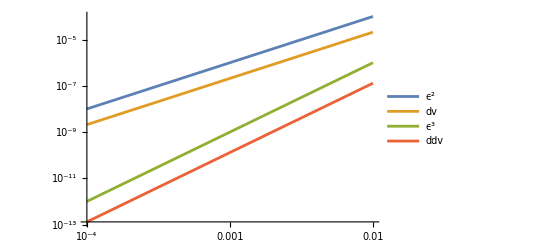

```mathematica
{n,b}={23,4};
vW=QRDecomposition[RandomReal[{-1,1},{n,b+1}]]⟦1⟧ᵀ;
v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
Map[Norm,{Wᵀ.W-IdentityMatrix[b],Wᵀ.v0,v0}];
v[ϵ_]:=(v0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
dv[ϵ_,u1_]:= W.u1(1+ϵ.ϵ)^(-1/2)-(v0+W.ϵ)(1+ϵ.ϵ)^(-3/2)ϵ.u1
ddv[ϵ_,u1_,u2_]:=(3(v0+W.ϵ)(1+ϵ.ϵ)^(-5/2)(ϵ.u1 )(ϵ.u2)
-W.u1(1+ϵ.ϵ)^(-3/2)ϵ.u2 -W.u2(1+ϵ.ϵ)^(-3/2)ϵ.u1 -(v0+W.ϵ)(1+ϵ.ϵ)^(-3/2)u1.u2
)
(* Tangent line and quadratic approximation *)
(* scaling behavior single direction *)
x0=RandomReal[{-1,1},b];
{u1,u2}=Map[Normalize,RandomReal[{-1,1},{2,b}]];
LogLogPlot[{
ϵ^2,
Norm[v[x0+ϵ u1]-(v[x0]+ϵ dv[x0,u1])],
ϵ^3,
Norm[v[x0+ϵ u1]-(v[x0]+ϵ dv[x0,u1]+1/2 ϵ^2 ddv[x0,u1,u1])]
},
{ϵ,10^-4,10^-2},
PlotLegends->{"ϵ^2","dv","ϵ^3","ddv"}
]
```

Checking that I have first and second derivatives correct in the two direction sense.

```mathematica
g={dv[x0,u1],dv[x0,u2]};
H=({{ddv[x0,u1,u1], ddv[x0,u1,u2]}, {ddv[x0,u2,u1], ddv[x0,u2,u2]}});
{α1,α2}=RandomReal[{-1,1},2];
(* Tangent line and quadratic approximation *)
(* scaling behavior single direction *)
TabView[{
"lin"->ContourPlot[ 
Norm[
v[x0+ϵ1 u1+ ϵ2 u2]-(v[x0]+{ϵ1,ϵ2}.g)
],
{ϵ1,-0.01,0.01},{ϵ2,-0.01,0.01},
PlotLegends->Automatic,
Contours->20],
"quad"->ContourPlot[ 
Norm[
v[x0+ϵ1 u1+ ϵ2 u2]-(v[x0]+{ϵ1,ϵ2}.g+1/2{ϵ1,ϵ2}.({ϵ1,ϵ2}.H))
],
{ϵ1,-0.01,0.01},{ϵ2,-0.01,0.01},
PlotLegends->Automatic,
Contours->20],
"slice"->LogLogPlot[{
ϵ^2,
Norm[v[x0+ϵ (α1 u1+α2 u2)]-(v[x0]+ϵ {α1,α2}.g )],
ϵ^3,
Norm[v[x0+ϵ (α1 u1+α2 u2)]-(v[x0]+ϵ {α1,α2}.g+1/2 ϵ^2 {α1,α2}.({α1,α2}.H))]
},
{ϵ,10^-4,10^-2},
PlotLegends->{"ϵ^2","lin","ϵ^3","quad"}]
}]
```

123

The Arnoldi process (with no initial scaling) is being defined on the surface of the n-1 dimensional unit sphere 𝒮_(m-1)=∂ℬ_m⊂ℝ^m.  Provided Wᵀ.v_0=0 and Wᵀ.W=I_b the function v:ℬ_b→𝒮_(m-1)⊂ℝ^m defined by 
	v[ϵ]=(v_0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
is a smooth parameterization of a b dimensional patch of 𝒮_(m-1).  The formula above give
	q_1(0) | = | v_0 |   |  
∂_j q_1(0) | = | W.e_j | = | w_j
∂_(j,k) q_1(0) | = | v_0(e_j.e_k) | = | δ_(j,k)v_0
These let us “start” AD computations for the Arnoldi process.

## AD Computation: Code vs linear algebra way

For A∈ℝ^(n×n)the Arnoldi process iteratively computes a partial decomposition
	A.Q_m=Q_m.H_m+γ_(m+1)q_(m+1)
starting from q_1∈ℝ^n with ||q_1||=1 where 
	Q_m=[q_1 | | | q_2 | | | … | | | q_m]
and (Q_m)ᵀ.Q_m=I_m and (Q_m)ᵀ.q_(m+1)=0_m and γ_(m+1)≥0 and ||q_(m+1)||=1. The sign condition on γ makes the process unique.  The process breaks down iff γ_(m+1)=0.  some I want to understand the behavior of γ_(m+1) on perturbed inputs.

The “code way” of computing sensitivities modifies the Arnoldi code to compute partial derivatives as you go. The “linear algebra” way of computing sensitivities differentiates the decomposition and solves for partial derivatives using the computed values.  
	A.dQ_m=dQ_m.H_m+dQ_m.H_m+dγ_(m+1)q_(m+1)+γ_(m+1)dq_(m+1)

### Linear algebra way overview

By construction, the iterative residual γ_(m+1)q_(m+1) is
	γ_(m+1)q_(m+1)=(I-Q_m.(Q_m)ᵀ)A.q_m
If we initialize with  
	q_1=(v_0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
then 
	q_1(0) | = | v_0 |   |  
∂_j q_1(0) | = | W.e_j | = | w_j
∂_(j,k) q_1(0) | = | v_0(e_j.e_k) | = | δ_(j,k)v_0

#### Linear algebra way First Derivatives: First Step

Proceed iteratively and differentiate
	γ_2 q_2=P_1.A.q_1
where P_1=I-Q_1.(Q_1)ᵀ=I-q_1⊗q_1
to get
	dγ_2 q_2+ γ_2 dq_2=dP_1.A.q_1+P_1.A.dq_1
I know dq_1 so I can compute A.dq_1.  I have already computed A.q_1
I know dP_1 since 
	dP_1=-dQ_1.(Q_1)ᵀ-Q_1.(dQ_1)ᵀ
Since q_2.q_2=1 we have dq_2.q_2=0 so
	dγ_2(q_2.q_2)+ γ_2(dq_2.q_2)=(dP_1.A.q_1+P_1.A.dq_1).q_2
and we get
	dγ_2=(dP_1.A.q_1+P_1.A.dq_1).q_2
Ignoring any cancellation for now we can finish the computation with
	 dq_2=(dP_1.A.q_1+P_1.A.dq_1-dγ_2 q_2)/γ_2

#### Linear algebra way First Derivatives: Induction

Proceed iteratively and differentiate
	γ_(m+1)q_(m+1)=P_m.A.q_m
where P_m=I-Q_m.(Q_m)ᵀ to get
	dγ_(m+1)q_(m+1)+ γ_(m+1)dq_(m+1)=dP_m.A.q_m+P_m.A.dq_m
I know dq_m so I can compute A.dq_m and
	dP_m=-dQ_m.(Q_m)ᵀ-Q_m.(dQ_m)ᵀ
Since q_(m+1).q_(m+1)=1 we have dq_(m+1).q_m=0 so
	dγ_(m+1)=(dP_m.A.q_m+P_m.A.dq_m).q_m
and
	 dq_(m+1)=(dP_m.A.q_m+P_m.A.dq_m-dγ_(m+1)q_m)/γ_(m+1)

So I can do this during the computation or after the computation! I am doing it after the initial Arnoldi computation.

```mathematica
{m,b}={23,5};
(* Create a surface patch parametrization *)
vW=QRDecomposition[RandomReal[{-1,1},{m,b+1}]]⟦1⟧ᵀ;
v0=vW⟦All,1⟧; W=vW⟦All,2;;b+1⟧;
v[ϵ_]:=(v0+W.ϵ)(1+ϵ.ϵ)^(-1/2)
(* Create a test matrix *)
A=RandomReal[{-1,1},{m,m}]; 
(* Compute Arnoldi process *) 
n=3;
{Q,H}=Arnoldi[A][v0,n];
(* Implement 1st derivative AD computation *)
(* Create storage for 1st derivatives *)
(* directions b are at the back *)
dQ=ConstantArray[0.0,{m,n+1,b}];
(* I do not need derivatives of all of H if I use *)
(*  Subscript[γ, k+1] Subscript[q, k+1] = (I - Subscript[Q, k].Subscript[Q, k] ᵀ)A.Subscript[q, k] *)
 (* I only need the subdiagonal γ and its derivatives *)
(* as always derivative directions are at the back *)
γ=Diagonal[H,-1];
dγ=ConstantArray[0.0,{n,b}];
(* Iterate through the first columns of dQ for all the directions *)
dQ⟦All,1,1;;b⟧=A.W⟦All,1;;b⟧;
(* Start filling in dγ using *)
(*  Subscript[dγ, k+1] Subscript[q, k+1] + Subscript[γ, k+1] Subscript[dq, k+1]  = (I - Subscript[Q, k].Subscript[Q, k] ᵀ)A.Subscript[dq, k] - (Subscript[dQ, k] Subscript[Q, k] ᵀ+Subscript[Q, k] Subscript[dQ, k] ᵀ).A.Subscript[q, k] *)
(* I am prestoring the already compute A.Subscript[q, 1:n] and precomputing A.Subscript[dq, 1]=A.W*)
(* for all the directions dq in W⟦All,1;;b⟧ *)
AQ=Q.H; 
dQ1 =W;
AdQ1=A.dQ1;
(* defining the RHS as data *)
QQ=Q⟦All,1;;k⟧;P=IdentityMatrix[m]-QQ.QQᵀ;
data = P.AdQ1 ;
data2=Table[(QQ.dQ1⟦All,{bb}⟧ᵀ+dQ1⟦All,{bb}⟧.QQᵀ).AQ⟦All,1⟧,{bb,1,b}]ᵀ;
bb=1;
Map[Dimensions,{data,data2}]
```

{{23,5},{23,5}}

Arggh! I have the structure all messed up.

```mathematica
Map[Dimensions,{Q,A,W}]
```

{{23,4},{23,23},{23,4}}

```mathematica
k=1;
Map[Dimensions,{ Q⟦All,1;;k⟧ᵀ,AdQ1⟦k⟧}]
```

{{1,23},{4}}

```mathematica
MatrixForm[H]
Diagonal[H,-1]
```

(-1.31381 | -0.210399 | -0.281173
3.09163 | -0.132936 | -0.33912
0. | 1.98141 | 0.564795
0. | 0. | 2.50912)

{3.09163,1.98141,2.50912}

```mathematica
MatrixForm[dH]
```

((0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.))

```mathematica
b
```

4

```mathematica
{Q,H}=Arnoldi[A][v0,n];

A.W;
A.Q;
```

```mathematica
{Q,H}=Arnoldi[A][b,n];
TableForm[{
{UpperTriangularMatrixQ[H,-1],OrthogonalMatrixQ[Q]},
{Dimensions[Q]=={m,n+1},Dimensions[H]=={n+1,n}},
Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}],
{Min[Diagonal[H,-1]],H⟦n+1,n⟧}
},TableHeadings->{{"Structure","Dimensions","Residuals","Subdiagonal"},None}]
```

```mathematica
ArnoldiAD1st[A_][{Q_,H_},W_]:= Module[
(* Assuming Wᵀ.Subscript[q, 1] = Subscript[0, b] and Wᵀ.W = Subscript[I, b] *)
(* Q and H are from Arnoldi code *)
{dQ1=A.W, },
]
```

#### Linear algebra way Second Derivatives: Induction

Start from 
	dγ_(m+1)q_(m+1)+ γ_(m+1)dq_(m+1)=dP_m.A.q_m+P_m.A.dq_m
and subscript the differentiation to get
	 (d_a γ_(m+1))q_(m+1)+ γ_(m+1)(d_a q_(m+1))=(d_a P_m).A.q_m+P_m.A.(d_a q_m)
Differentiate with the LHS respect to b to get 
	(d_ab γ_(m+1))q_(m+1)+(d_a γ_(m+1))(d_b q_(m+1))
+ γ_(m+1)(d_ab q_(m+1))+  (d_b γ_(m+1))(d_a q_(m+1))
Differentiate the RHS with respect to b to get
	(d_ab P_m).A.q_m+(d_a P_m).A.(d_b q_m)
+P_m.A.(d_a q_m)+(d_b P_m).A.(d_b q_m)
The RHS minus the first derivative terms (d_a γ_(m+1))(d_b q_(m+1))+(d_b γ_(m+1))(d_a q_(m+1)) are known. 
Data=(d_ab P_m).A.q_m+(d_a P_m).A.(d_b q_m)+P_m.A.(d_a q_m)+(d_b P_m).A.(d_b q_m)-
((d_a γ_(m+1))(d_b q_(m+1))+(d_b γ_(m+1))(d_a q_(m+1)))
Since q_(m+1).q_(m+1)=1 we have 
	d_a q_(m+1).q_(m+1) | = | 0
d_b q_(m+1).q_(m+1) | = | 0
d_ab q_(m+1).q_(m+1) | = | -d_bq_(m+1).d_a q_(m+1)
Since
	(d_ab γ_(m+1))q_(m+1)+ γ_(m+1)(d_ab q_(m+1))=Data
we can determine d_ab γ_(m+1)by taking the dot product with q_(m+1) through
	(d_ab γ_(m+1)) | = | Data.q_(m+1)-γ_(m+1)(d_ab q_(m+1)).q_(m+1)
d_ab γ_(m+1) | = | Data.q_(m+1)+γ_(m+1)(d_a q_(m+1)).(d_b q_(m+1))
once this is determined the last step is to compute d_ab q_(m+1) through
	 d_ab q_(m+1)=(Data-(d_ab γ_(m+1))q_(m+1))/γ_(m+1)

So I can do this during the computation or after the computation!